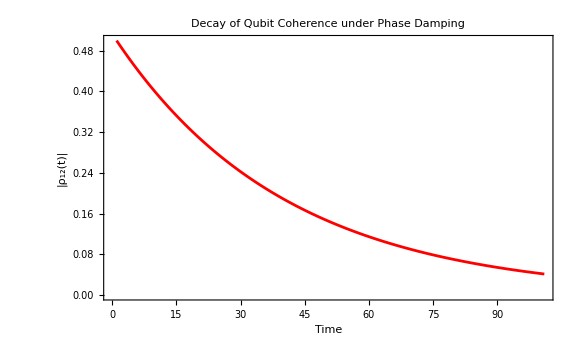

```mathematica
(*Decoherence of a Qubit under Phase Damping*)
(*Objective*)(*Simulate the effect of phase damping on a qubit's density matrix.We observe the decay of the off-diagonal element (coherence).*)

(* ::Section::*)(*Initial State Setup*)
(*Define initial pure state|ψ⟩=(|0⟩+ |1⟩)/√2*)psi={1,1}/Sqrt[2];
(*Density matrix ρ(0)= |ψ⟩⟨ψ|*)
rho0=Outer[Conjugate[#1]*#2&,psi,psi];

(* ::Section::*)
(*Kraus Operators for Phase Damping*)

KrausOperators[p_]:={{{1,0},{0,Sqrt[1-p]}},{{0,0},{0,Sqrt[p]}}};

(* ::Section::*)
(*Density Matrix Evolution Function*)

RhoT[rho_,p_]:=Module[{Ks},Ks=KrausOperators[p];
Total[Table[ConjugateTranspose[Ks[[i]]].rho.Ks[[i]],{i,Length[Ks]}]]];

(* ::Section::*)
(*Time Evolution and Coherence Plot*)

(*Parameters*)
γ=0.5; (*phase damping rate*)
tmax=10;
dt=0.1;
times=Range[0,tmax,dt];

(*Compute evolved density matrices*)
rhos=Table[RhoT[rho0,1-Exp[-γ*t]],{t,times}];

(*Extract|ρ₁₂(t)|for each time*)
coherences=Abs[#[[1,2]]&/@rhos];

(*Plot the coherence decay*)
ListLinePlot[coherences,Frame->True,FrameLabel->{"Time","|ρ₁₂(t)|"},PlotLabel->"Decay of Qubit Coherence under Phase Damping",PlotStyle->Red,ImageSize->Large]
```